```mathematica
SetDirectory[NotebookDirectory[]];
If[Count[$Path,(Directory[]<>"\\libs")]==0,AppendTo[$Path,(Directory[]<>"\\libs")]];
```

```mathematica
Needs["cellComplex`"];
```

Needs::nocont: Context "cellComplex`" was not created when Needs was evaluated.

```mathematica
ClearAll[ivd,ivdE,ivdG,ivdV,ivdGoodE,img2Bndry,img2IVD,img2MA,makeFigsFromImgFile,showIVD,showBoundaryForIVD,showMA,showBoundaryForMA]
```

#### Helpers

given a point in image space, return the pixel containing it. (x & y need to be swapped to index into the 2d-array-represented image)

```mathematica
findpix={#2,#1}&@@Floor[#+0.5]&;
```

```mathematica
findpix[{1,2.1}];
```

pixel out-of-bound of image?

```mathematica
outbound[i_,p_]:=p⟦1⟧>Dimensions[i]⟦1⟧||p⟦1⟧<1||p⟦2⟧>Dimensions[i]⟦2⟧||p⟦2⟧<1;
```

return the pixel value

```mathematica
pixval[i_,p_]:=If[outbound@@{i,p},0,i⟦p⟦1⟧⟧⟦p⟦2⟧⟧]
```

Visualize IVD and MA

```mathematica
showBoundaryForMA=Graphics[Line[#]]&;
showMA=Graphics[GraphicsComplex[#⟦1⟧,{Green,Thick,Line[(*ivd⟦2⟧*)#⟦2⟧]}]]&;
```

```mathematica
Complement[{1,2,3},{}]
```

{1,2,3}

```mathematica
showBoundaryForIVD=Graphics[Point[#]]&;
showIVD[ivd_]:=Module[{islandVts},
islandVts=Complement[Range[ivd⟦1⟧//Length],ivd⟦2⟧//Flatten//Union];
Graphics[{
If[Length@islandVts>0,{Red,Point@ivd⟦1⟧⟦islandVts⟧}],
GraphicsComplex[ivd⟦1⟧,{Blue,Thick,Line[(*ivd⟦2⟧*)ivd⟦2⟧]}]
}]
]
```

Subdivide each edge by placing n extra vts on edge evenly.
Return {all vts (including old + new), all new edges}.

```mathematica
tessEdges[vts_,edges_,n_]:=Module[{
newvts,newedges,w,u,v,VonE},
(*generate weights for new vts*)
w=#*1./(n+1)&/@(Drop[Range[n+1],-1]);
(*list of vts on an edge*)
Reap[(
{u,v}=vts⟦#⟧;
VonE={1.-#,#}.{u,v}&/@w;
Sow@#&/@VonE;
VonE={u}~Join~VonE~Join~{v};
)&/@edges
]⟦2⟧⟦1⟧
];
```

Generate IVD from input: samples, and binary image

```mathematica
genIVD[s_,img_]:=Module[
{voro,voroV,voroE,isInside,insideVids,ivdV,ivdE,old2newVidMap},
voro=VoronoiMesh[s];
voroV=MeshCoordinates@voro;
isInside=pixval[img,findpix[voroV⟦#⟧]]>0&/@Range[voroV//Length];
insideVids=Pick[Range[voroV//Length],isInside];
ivdV=voroV[[insideVids]];
(*remember how old v id -> new v id*)
old2newVidMap[___]=Null;
MapThread[(old2newVidMap[#1]=#2)&,{insideVids,Range[insideVids//Length]}];
(*re-index vertices in each inside edge*)
voroE=(#⟦1⟧)&/@MeshCells[voro,1];
ivdE=Reap[
If[isInside⟦#⟦1⟧⟧&&isInside⟦#⟦2⟧⟧,Sow[old2newVidMap/@#]]&/@voroE
]⟦2⟧⟦1⟧;

Return[{ivdV,ivdE}];
];
```

Image array -> boundary V and E

```mathematica
img2Bndry[iarr_,tessn_]:=Module[{
cc2,boundaryEdges,bndryEdgeIndices,boundaryVts,newVtsOnVoroE
},
(*image array -> a 2 cc*)
cc2=buildCC2D[iarr,"pixelCorner"];

(*extract boundary elements*)
bndryEdgeIndices=getExteriorEdges[cc2];
boundaryEdges=cc2⟦1⟧⟦#⟧&/@bndryEdgeIndices;
boundaryVts=getExteriorVts[cc2];
newVtsOnVoroE=If[tessn>0,tessEdges[cc2⟦1⟧,bndryEdgeIndices,tessn],{}];
boundaryVts=boundaryVts~Join~newVtsOnVoroE;

Return[{boundaryVts,boundaryEdges}];
];
```

```mathematica
(*testBndryV=img2Bndry[imgBin,1][[1]];
genIVD[testBndryV,imgBin]*)
```

Boundary V + image array  -> return IVD

```mathematica
bndry2IVD[bndryV_,iarr_]:=Module[{
ϵ=1*^-8,
boundaryVts,
ivd,
ivdV,ivdE,ivdGoodE
},

(*generate IVD*)
ivd=genIVD[bndryV,iarr];

(*throw away 0-length edges (for vis purpose, cuz they mess up rendering)*)
{ivdV,ivdE}=ivd;
ivdGoodE=Reap[(If[EuclideanDistance@@ivd⟦1⟧⟦#⟧>ϵ,Sow@#])&/@ivdE]⟦2⟧/.{x_,___}->x;
ivd={ivdV,ivdGoodE};

Return[ivd];
];
```

```mathematica
(*bndry2IVD[testBndryV,imgBin]*)
```

Image array + tesselation number n + a transformation function t -> return IVD related figure

```mathematica
img2IVD[iarr_,tessn_,t_]:=Module[{
ϵ=1*^-8,
boundaryVts,boundaryEdges,
ivd,
ivdV,ivdE,ivdGoodE,
ivdG,bndryG,fineBndryG
},

(*extract boundary elements*)
{boundaryVts,boundaryEdges}=img2Bndry[iarr,tessn];

(*from boundary samples generate IVD*)
ivd=bndry2IVD[boundaryVts,iarr];

(*apply any transformation*)
ivd⟦1⟧=t/@ivd⟦1⟧;
boundaryVts=t/@boundaryVts;
boundaryEdges=t/@#&/@boundaryEdges;

(*generate graphics objects*)
fineBndryG=Graphics[Point[boundaryVts]];
ivdG=Graphics[GraphicsComplex[ivd⟦1⟧,{Darker@Yellow,Thick,Line[(*ivd⟦2⟧*)ivd⟦2⟧]}]];

Return[{ivd,boundaryVts}];
];
```

```mathematica
(*img2IVD[imgBin,2,Identity][[1]]//showIVD;*)
```

Image array -> the MA of boundary samples

```mathematica
img2MA[iarr_,tessn_,t_]:=Module[{
ϵ=1*^-8,
boundaryVts,boundaryEdges,fineBndryVts,fineBndryEdges,
ivd,
ivdV,ivdE,ivdGoodE,
ivdG,bndryG,fineBndryG
},

(*extract boundary elements*)
{fineBndryVts,fineBndryEdges}=img2Bndry[iarr,tessn];
{boundaryVts,boundaryEdges}=img2Bndry[iarr,0];

(*from boundary samples generate IVD*)
ivd=bndry2IVD[fineBndryVts,iarr];

(*apply any transformation*)
ivd⟦1⟧=t/@ivd⟦1⟧;
boundaryVts=t/@boundaryVts;
boundaryEdges=t/@#&/@boundaryEdges;
fineBndryVts=t/@fineBndryVts;
fineBndryEdges=t/@#&/@fineBndryEdges;

(*generate graphics objects*)
bndryG=Graphics[Line[boundaryEdges]];
fineBndryG=Graphics[Point[fineBndryVts]];
ivdG=Graphics[GraphicsComplex[ivd⟦1⟧,{Darker@Blue,Thick,Line[(*ivd⟦2⟧*)ivd⟦2⟧]}]];

Return[{ivd,boundaryEdges}];
];
```

Read an image -> return the boundary samples, VD, IVD and MA

```mathematica
makeFigsFromImgFile[filename_,tessn_]:=Module[{
img,maTessN,
ivd,bndryV,ma,bndryLines,
ivdG,maG,bndryG,fineBndryG
},
(*read in an image -> a 2 cc*)
img=PNGtoGray[filename];
img=threshold[img,100];

{ivd,bndryV}=img2IVD[img,tessn,Identity];
{ivdG,fineBndryG}={showIVD@ivd,showBoundaryForIVD@bndryV};
maTessN=Max[10,tessn+1];
{ma,bndryLines}=img2MA[img,maTessN,Identity];
{maG,bndryG}={showMA@ma,showBoundaryForMA@bndryLines};

Return[
GraphicsColumn[{
(*Histogram[EuclideanDistance@@ivd⟦1⟧⟦#⟧&/@ivd⟦2⟧,100],
Histogram[EuclideanDistance@@ivd⟦1⟧⟦#⟧&/@ivdGoodE,100],*)
Show[(*bndryG*)fineBndryG,ivdG],
Show[bndryG,maG]
},
Background->White]
];
];
```

#### 2D Voro

Read in an image

```mathematica
filename="test_img\\test.png";
img=PNGtoGray[filename];
(*img=PNGtoGray["test_img\\voronoi_test_2.png"];*)
(*img=PNGtoGray["test_img\\horse_64.png"];*)
(*img=PNGtoGray["test_img\\square.png"];*)
```

```mathematica
imgBin=threshold[img,100];
```

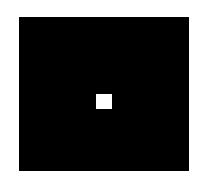

```mathematica
showBinaryImage[imgBin]
```

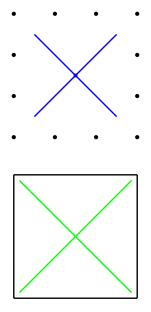

```mathematica
makeFigsFromImgFile[filename,2]
```

#### Manipulate tool for test case construction

```mathematica
DynamicModule[{
computeAll,computeIVD,computeMA,computeDT,reset,
w=5,h=5,showivd,showma,(*widgets*)
p={1,1},pval,img,imgData={},img2,
trans=TranslationTransform[{-0.5,-0.5}],
ivdBndry,maBndry,ivd=Null,ma=Null,dtG
},
reset[w_,h_]:=Module[{},
img=Image[Table[0,{i,1,h},{j,1,w}],ImageSize->Small];
ivd=Null;ma=Null;
];
computeIVD[imgData_,tessN_]:=Module[{
},
{ivd,ivdBndry}=img2IVD[imgData,tessN,trans];
];
computeMA[imgData_]:=Module[{
},
{ma,maBndry}=img2MA[imgData,10,trans];
];
computeDT[pts_]:=Module[{},
dtG=HighlightMesh[DelaunayMesh[pts],{Style[2,Opacity[.5]]}];
];
computeAll[tessN_]:=Module[{},
imgData=img//ImageReflect//ImageData;
If[(imgData//Flatten//Total)>0,
computeIVD[imgData,tessN];
computeMA[imgData];
computeDT[ivdBndry];
];
];
reset[w,h];
img2=img;

Manipulate[
ClickPane[
Show@Join[
{ArrayPlot[img//ImageData,
ColorFunction->(If[#≥0.5,RGBColor[1,1,1,1],If[showimg,RGBColor[0,0,0,1],RGBColor[1,1,1,1]]]&),ColorFunctionScaling->False,
If[showmesh,Mesh->All,Mesh->None],ImageSize->Large
]},
If[ma=!=Null&&showma,{ma//showMA(*,maBndry//showBoundaryForMA*)},{}],
If[ivd=!=Null&&showivd,{ivd//showIVD(*,ivdBndry//showBoundaryForIVD*)},{}],
If[ivd=!=Null&&showdt,{dtG},{}]
]
,
(
p=IntegerPart[#+1];
pval=PixelValue[img,p];
img=If[pval≥0.5,
ReplacePixelValue[img,p->0.0],
ReplacePixelValue[img,p->1.0]];computeAll[tessN]
)&
]
,{w,5},{h,5}
,{{showivd,False},{True,False}},{{showma,False},{True,False}},{{showdt,False},{True,False}},{{showmesh,True},{True,False}},{{showimg,True},{True,False}}
,Button["reset",reset[w,h]]

,{tessN,0}
]
]
```

## Examples

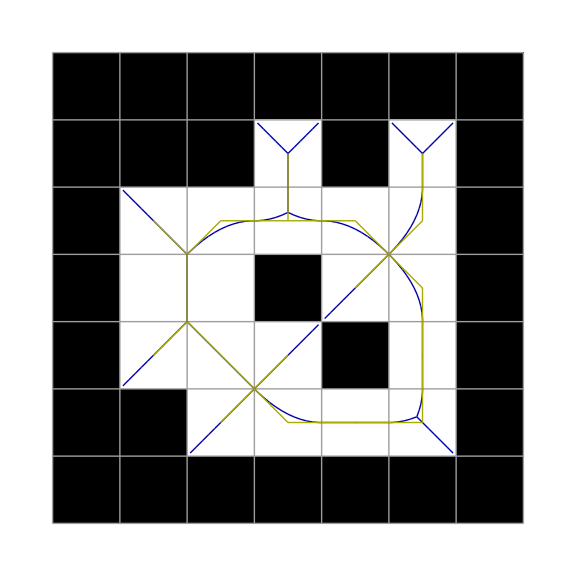

-Graphics-